```mathematica
SetDirectory[NotebookDirectory[]];
x=Import["output_cube100_min50.txt"];
dt=StringSplit[x,"\n"];
dt=ToExpression[#]&/@dt;
dt//Dimensions
```

{102512}

```mathematica
all=dt//Length;dt=Select[dt,#>0&];
Print[{all,dt//Length}]
```

{102512,102042}

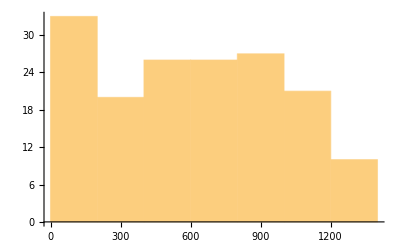

```mathematica
numNeurons=Sort[Tally[dt],#1[[2]]>#2[[2]]&][[;;,2]];
Histogram[numNeurons]
```